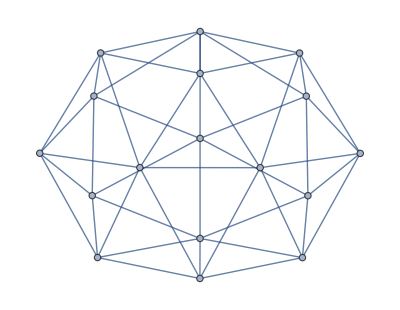

```mathematica
g=Graph[plantri[[8]]]
```

```mathematica
interestingVertices={7,15,17,12,13,14}
```

{7,15,17,12,13,14}

```mathematica
interestingEdges=Select[EdgeList[g],MemberQ[interestingVertices,#[[1]]]&& MemberQ[interestingVertices,#[[2]]]&]
```

{7<->13,7<->14,7<->15,12<->17,12<->14,12<->13,13<->14,14<->17,14<->15,15<->17}

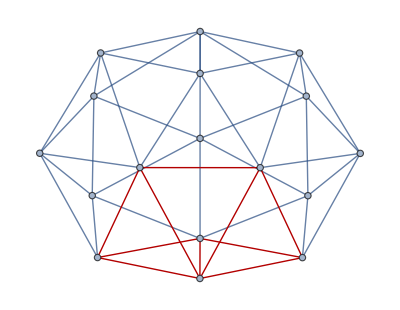

```mathematica
Graph[g,GraphHighlight->interestingEdges]
```

```mathematica
ExamineGraph[g,interestingEdges]
```